Adapted from Jiwon Yun’s notebook, "entropy"

## Preliminary

```mathematica
SetDirectory["~/projects/mcfgcky2_repos/"]; (* John's laptop *)
```

```mathematica
Off[Graph::optx];  (* Turn off warnings about graph options *)
```

```mathematica
<<Combinatorica` (* was <<DiscreteMath`Combinatorica`;  *)
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

I increased WorkingPrecision in CalculateZ to avoid rounding off some very small Z values to zero, which was happening in the 6th sentence of the K-H stimuli. Turn off the complaining about how that FindRoot call is using arguments with lower precision than that. Also turn off warnings about line search.

```mathematica
Off[FindRoot::precw]; Off[FindRoot::bddir]
```

## Normalize Grammar

note that this function does not divide by the sum of the weights of rules sharing the same LHS; rather it preserves the given weight as a Mathematica fraction. This is key for deriving Z values other than 1.

```mathematica
ChartToGrammar[ch_,startsymbolregexp_ :"S.*"] := Module[{nonterminals,terminals},
LhsRhsSymbol[line_] :=Switch[Length[line],
6, {Part[line,4],Part[line,6]},   (* terminal line *)
7,{Part[line,4],Part[line,6]},    (* unary with string rewriting recipe *)
8,{Part[line,4],Part[line,6],Part[line,7]}, (* binary *)
_,{}];

LhsSymbol[line_] :=Switch[Length[line],
6, {Part[line,4]},
7,{Part[line,4]},
8,{Part[line,4]},
_,{}];

kind[f_] := DeleteDuplicates[Flatten[f /@ ch ]];

nonterminals = kind[LhsSymbol];
terminals = Complement[kind[LhsRhsSymbol],kind[LhsSymbol]];

markup[line_] :=Switch[Length[line], (* throw away recipe *)
6, {"Preterminal",Part[line,1]/Part[line,3],Part[line,4],Part[line,6]},
7,{"Unary",Part[line,1]/Part[line,3],Part[line,4],Part[line,6]},
8,{"Binary",Part[line,1]/Part[line,3],Part[line,4],Part[line,6],Part[line,7]}, 
_,{}];
Return[{ First[Select[nonterminals,StringMatchQ[#,RegularExpression[startsymbolregexp]]&]],(* assume it's the first one *)
              nonterminals,   (* second and third components constitute a disjoint set of vertex labels *)
              terminals,
		markup/@ch (* was : divide /@ vulgar *)
	}]
];
```

This was the procedure from Hale 2003 , 2006

```mathematica
LocallyNormalize[grammar_List]:= Module[{start,nonterminals,terminals,rules,sums,both,divide},
{start,nonterminals,terminals,rules}=grammar;
sums=Function[symbol,Fold[Plus,0,Part[#,2]&/@Select[rules,Part[#,3]==symbol&]]]/@nonterminals;

both=Join[nonterminals,terminals];

divide[wrule_]:=Module[{originalweight,nonterminalnumber,nonterminalsum},originalweight=Part[wrule,2];
nonterminalnumber=FromDigits[FromDigits[Position[both,Part[wrule,3]]]];
nonterminalsum=N[originalweight/(sums[[nonterminalnumber]]),MachinePrecision]; (* become machine-precision *)
ReplacePart[wrule,2->nonterminalsum]];

Return[{start,nonterminals,terminals,(divide/@rules)}]
];
```

## Create Graph Projection

```mathematica
GraphProjection[g_ ]:= Module[{start,nonterminals,terminals,vertices,rules,edges,i},
	{start,nonterminals,terminals,rules} =g;
	vertices = Join[nonterminals,terminals];
	edges ={};
	
	lookup[rulenum_,eltnum_] := FromDigits[FromDigits[Position[vertices,rules[[rulenum]][[eltnum]]]]];

	For[i=1,i≤ Length[rules],i++,
	    Switch[First[rules[[i]]],
	 "Preterminal",AppendTo[edges,{lookup[i,3],lookup[i,4]}],
	"Unary",AppendTo[edges,{lookup[i,3],lookup[i,4]}],
	"Binary",AppendTo[edges,{lookup[i,3],lookup[i,4]}];
			   AppendTo[edges,{lookup[i,3],lookup[i,5]}]
	]
	];

Return[FromOrderedPairs[edges]]
];
```

## Strongly - Connected Components

Whereas Cormen, Leisersohn and Rivest give just one, more complicated function, I split things up into two different DFS functions. One records finishing times while the other keeps track of "depth first forests" originating from a given start point. Node numbers for vertices in these forests are stored on the lastfound list

```mathematica
ftimeDFSVisit[u_Integer] :=
		Module [{}, (* recursive helper function for ftimeDFS, below *)
		color[[u]] = Gray;
			Scan[ (If[color[[#]]==White,
				ftimeDFSVisit[#];
				color[[u]]=Black];
				   t++;
			   ftime[[u]]= t;
		)&,e[[u]]
			]
		]
```

```mathematica
ftimeDFS[g_Graph] := (* this function computes a list of finishing times in a DFS traversal of g. p541 of Cormen, Leisersohn & Rivest *)
	Block[{color=Table[White,{V[g]}],t=0,e=ToAdjacencyLists[g],ftime=Table[-1,{V[g]}],$RecursionLimit = Infinity},
	(* for each vertex, check if we've been there before, otherwise call ftimeDFSVisit *)
	Do[If[color[[vert]]==White,ftimeDFSVisit[vert]],{vert,1,V[g]}];
	
	Return[Sort[Range[1,V[g]],(ftime[[#1]]>ftime[[#2]])&]] (* Descending order order on times = Ascending whole numbers *)
	]
```

```mathematica
myDFSVisit[u_Integer] := Module [{}, (* recursive helper function for myDFS, below *)
	AppendTo[lastfound,u];
	color[[u]] = Gray;
	Scan[ (If[color[[#]]==White,
			myDFSVisit[#];
			color[[u]]=Black])&,e[[u]]
		]
]
```

```mathematica
myDFS[graph_Graph,orderedvertices_List] := (* same algorithm but keep track of all vertices in what CLR call the Depth-first Forest *)
	Block[{color=Table[White,{V[graph]}],e=ToAdjacencyLists[graph],lastfound={},$RecursionLimit = Infinity},
	(If[color[[#]]== White,myDFSVisit[#];AppendTo[SCCs,lastfound];lastfound={}])& /@ orderedvertices
	]
```

```mathematica
getSCCs[graph_Graph] := 
Block[{SCCs={}},
	myDFS[ReverseEdges[graph],ftimeDFS[graph]];
	Return[Reverse[SCCs]]
	]
```

## Calculate Inside Probabilities

page 146 of Nederhof & Satta (2008) Computing Partition Functions of PCFG

```mathematica
CalculateZ[grammar_,graphprojection_,sortedSCCs_] := Module[{myZ,start,nonterminals,terminals,rules,tbl,vertices,vertexNumber,vertexLabel,eqns,vars,zValues},
{start,nonterminals,terminals,rules} =grammar;
vertices = Join[nonterminals,terminals]; (* this is the ordering used in GraphProjection *)

(* lookup table maps from a given nonterminal number to all the rules sharing that nonterminal *)
tbl = Function[nt,Select[rules,Part[#,3]==nt&]]/@ nonterminals;

(* Initialize the list of Z values as 0 *)
myZ=Table[0,{V[graphprojection]}];

(* vertexNumber -> x_vertexNumber *)
XVariable[n_]:=Subscript[x,n];

vertexNumber[v_String] := FromDigits[FromDigits[Position[vertices,v]]]; (* just as in GraphProjection *)
vertexLabel[v_Integer] := vertices[[v]];

(* Recursive Function Falpha: Falpha[scc,rhs] calculates the value of f_a for the given scc, following the instruction in Nederhof & Satta (2008) p.146 *)
(* caller: Expr *)
Falpha[scc_,rhs_]:= Module[{},
If[rhs=={},
Return[1], (* (22) f_epsilon = 1 *)
If[MemberQ[terminals,vertexLabel[First[rhs]]],Return[Falpha[scc,Rest[rhs]]], (* (23) f_ab = f_b, if a is terminal *)
If[!MemberQ[scc,First[rhs]],
Return[myZ[[First[rhs]]]*Falpha[scc,Rest[rhs]]],(* (24) f_Bb = Z(B) * f_b, if B is not a member of the scc *)
Return[XVariable[First[rhs]]*Falpha[scc,Rest[rhs]]] (* (25) f_Bb = x_i * f_b, if B is a member of the scc *)
];
];
];
];

(* Function Expr: Expr[scc,vertex] gives a polynomial expression for each vertex in the scc, which eventually comprises Eqns *)
Expr[scc_,vertex_]:=Module[{myValue,weight,rhs,relevantRules},
If [MemberQ[terminals,vertexLabel[vertex]],Return[-XVariable[vertex]+1]];

(* otherwise... *)
myValue=-XVariable[vertex];

Scan[Function[r,weight = r[[2]];
	rhs = vertexNumber /@ Switch[First[r],"Binary",{r[[4]],r[[5]]},_,{r[[4]]}];
	myValue+=weight*Falpha[scc,rhs]],tbl[[vertex]]];

Return[myValue];
];

Vars[scc_] := Module[{poly},
	poly=Expr[scc,#]&/@ scc;
	Return[Variables[poly]]
];

Eqns[scc_]:= (Expr[scc,#]==0)&/@scc;

(* For each scc, calculate the Z value of all the vertices in it *)
Scan[Function[myBucket,If [Length[myBucket]==0, 
(* Case 0: the scc is empty -> something is wrong. *)
Print["Fail: The scc is empty",i], (* Jiwon: break here!! *)

(* Case 1: otherwise we can calculate the inside probability of each node in the scc! *)
eqns=Eqns[myBucket];
vars=Vars[myBucket];
zValues=vars/.FindRoot[eqns,({#,0}&/@vars),WorkingPrecision->16 (* MachinePrecision+2 *)]; (* motivated by sentence 6 *)
For[j=1,j<=Length[vars],j++, 
(* [vars[[j]][[2]]] = subscript number = vertex number *)
If[vars[[j]][[2]]==0,Print[eqns," got set to zero. increase WorkingPrecision?"];Abort[]];
(* Print["node ",vars[[j]][[2]]," Z=",zValues[[j]]];*)
myZ[[vars[[j]][[2]]]]=zValues[[j]]; 
]
]
],sortedSCCs];

Return[myZ]
];
```

## Tilt by Z

```mathematica
TiltGrammar[g_,z_]:= Module[{start,nonterminals,terminals,rules,amount},
	{start,nonterminals,terminals,rules} =g;
	vertices = Join[nonterminals,terminals];
	vertexNumber[v_String] := FromDigits[FromDigits[Position[vertices,v]]]; (* just as in GraphProjection *)

	zParent[lhs_String] := z[[vertexNumber[lhs]]];
         zChildren[rhs_List] := Fold[Times,1,Function[sym,If[MemberQ[terminals,sym],1,z[[vertexNumber[sym]]]]]/@rhs];

	       TiltRule[wrule_] := Module[{originalprob,lhs,rhs},
	originalprob = Part[wrule,2];
	lhs =Part[wrule,3];
	rhs = Switch[Part[wrule,1],"Binary",{Part[wrule,4],Part[wrule,5]},_,{Part[wrule,4]}];
	If[zParent[lhs]==0,Print["couldn't find a z for ",lhs," number ",vertexNumber[lhs]];Abort[]];
	amount = zChildren[rhs]/zParent[lhs];
	(*If[Abs[1-amount]>10^-10,Print["tilting by ",amount]];*)
	ReplacePart[wrule,2-> (originalprob*amount)]
	];

	Return[{start,
                      nonterminals,
                      terminals,
	             TiltRule/@rules}]
];
```

## Entropy of Grammar

```mathematica
littleh[g_]:= Module[{start,nonterminals,terminals,rules,Eta},
			{start,nonterminals,terminals,rules} =g;

			Eta[p_]:=-p*Log2[p];(* is there a better name? *)

			Return[
				Function[nt,
					Fold[Plus,0,Eta[Part[#,2]]&/@ Select[rules,Part[#,3]==nt& ]]
		                    ] /@ nonterminals
				]
			
			];
```

```mathematica
fertilitymatrix[g_] := Module[{start,nonterminals,terminals,rules,idx,a,updateA},
			                    {start,nonterminals,terminals,rules} =g;
					idx[nt_String] := FromDigits[FromDigits[Position[nonterminals,nt]]];
					a=ConstantArray[0,{Length[nonterminals],Length[nonterminals]}];

					updateA[r_] :=Module[{prob,lhs},
	                                              prob = Part[r,2];
						lhs =Part[r,3];
						If[MemberQ[nonterminals,Part[r,4]],a[[idx[lhs]]][[idx[Part[r,4]]]] += prob];

						If [Part[r,1]=="Binary" &&MemberQ[nonterminals,Part[r,5]],a[[idx[lhs]]][[idx[Part[r,5]]]] += prob] 
					];
					Scan[updateA,rules];
					Return[a]
];
```

```mathematica
entropyOfGrammar[g_] := Module[{start,nonterminals,terminals,rules,idx,fert,h,spectralradius,everybody},
			                    {start,nonterminals,terminals,rules} =g;
					idx[nt_String] := FromDigits[FromDigits[Position[nonterminals,nt]]];
					h = littleh[g];
					fert = fertilitymatrix[g];

					spectralradius =Max[Abs/@Eigenvalues[fert]];
					If[spectralradius > 1,Print["entropyOfGrammar: grammar not consistent"]];

					everybody=(Inverse[IdentityMatrix[Length[nonterminals]]-fert]) . h;
					(* Return[{everybody[[idx[start]]],everybody}] *)
					everybody[[idx[start]]]
];
```

## End - to - End

ah-singular.m is a Mathematica list of strings encoding the Keenan Hawkins stimuli from their 1974 study. There are 24 stimuli total.

```mathematica
<<ah-singular.m  (* keenanhawkins with all NPs made singular *)
```

subjobj.m is a Mathematica list of strings encoding subject and object -extracted RCs a la Just and Carpenter. 2 stimuli total.

```mathematica
<< subjobj.m
```

{{the,reporter,who,sent,the,photographer,to,the,editor,hoped,for,a,good,story},{the,reporter,who,the,photographer,sent,to,the,editor,hoped,for,a,good,story}}

korean.m is a Mathematica list of strings encoding the stimuli in Yun/Hale/Whitman 2010. There are 8 stimuli total.

```mathematica
<<korean.m  (* creates a list of lists named "korean" *)
```

nameOfCoordinate indexes the filenames created by getChartsand other functions below

```mathematica
nameOfCoordinate[sentencenumber_,prefixnumber_] :=
FileNameJoin[{$TemporaryDirectory, (* put it in /tmp/m on Mac OS X *)
StringJoin["prefix",ToString[sentencenumber],"-",ToString[prefixnumber],".chart"]}]
```

getCharts calls the MCFG parser to create all the prefix<Sentence>-<Prefix>.chart files using “unconditionedgrammarfilename” (which should be: “grammars/wmcfg/larsonian1.wmcfg”) or perhaps “grammars/wmcfg/jpr-fig13.wmcfg”

```mathematica
getCharts[unconditionedgrammarfilename_,sentences_List] := Module[{cleanupEpsilon= "sed -e 's/\" \"/EMPTY/'",fragstring,dest,cmd},
	interdigitate[a_String,b_String]:= If[a=="",b,If[b=="",a,a<>" "<>b]];

	For[sentencenumber=1,sentencenumber≤Length[sentences],sentencenumber++,
		For[prefixnumber =1,prefixnumber≤ Length[sentences[[sentencenumber]]],prefixnumber++,
		fragstring= Fold[interdigitate,"",Take[sentences[[sentencenumber]],prefixnumber]];
		dest =nameOfCoordinate[sentencenumber,prefixnumber];
		 cmd  = StringJoin["./mcfg_nt " ,unconditionedgrammarfilename," -p \"",fragstring,"\" | ",cleanupEpsilon," > ",dest];
		PrintTemporary[cmd];
		Run[cmd];
		
		]
	]
]
```

```mathematica
getUnlexicalizedCharts[unconditionedgrammarfilename_,sentences_List] := Module[{cleanupEpsilon= "sed -e 's/\" \"/EMPTY/'",fragstring,dest,cmd,postprocess,unlexicalizer},
	interdigitate[a_String,b_String]:= If[a=="",b,If[b=="",a,a<>" "<>b]];

	For[sentencenumber=1,sentencenumber≤Length[sentences],sentencenumber++,
		For[prefixnumber =1,prefixnumber≤ Length[sentences[[sentencenumber]]],prefixnumber++,
		fragstring= Fold[interdigitate,"",Take[sentences[[sentencenumber]],prefixnumber]];
		dest =nameOfCoordinate[sentencenumber,prefixnumber];
		
		(* the light gray colored lines below do the unlexicalizing *)
		postprocess=StringJoin["./unlexicalize.csh ",ToString[prefixnumber]];
		PrintTemporary[postprocess];
		Run[postprocess];

		unlexicalizer=StringJoin["unlexicalize",ToString[prefixnumber],".sed"];
		cmd  = StringJoin["./mcfg_nt " ,unconditionedgrammarfilename," -p \"",fragstring,"\" | ",cleanupEpsilon," | sed -E -f ",unlexicalizer," | sort -k4 | uniq > ",dest];

		PrintTemporary[cmd];
		Run[cmd];
		
		]
	]
]
```

This re-creates all the prefix grammars for a given set of examples:

```mathematica
getUnlexicalizedCharts["grammars/wmcfg/korean.wmcfg",korean]     (* change me! *)
```

```mathematica
getCharts["grammars/wmcfg/jpr-fig13.wmcfg",subjobj]
```

```mathematica
getCharts["grammars/wmcfg/larsonian1.wmcfg",Take[keenanhawkins,4]]
```

GloballyNormalize uses the functions defined above, especially CalculateZ

```mathematica
GloballyNormalize[grammar_List] := Module[{graph,SCCs,z},
graph=GraphProjection[grammar];
SCCs = getSCCs[graph];
z = CalculateZ[grammar,graph,SCCs];
Return[TiltGrammar[grammar,z]]
]
```

newStyle, oldStylecompute the entropy of a grammar after first Normalizeing in one way or the other

```mathematica
newStyle[filename_] := Module[{grammar,graph,SCCs,z,gprime},
grammar = ChartToGrammar[Import[filename,"Table"]]; (* add regexp here for custom start symbol *)
gprime = GloballyNormalize[grammar];
entropyOfGrammar[gprime]
];
```

```mathematica
oldStyle[filename_] := Module[{grammar,graph,SCCs,z,gprime},
grammar = LocallyNormalize[ChartToGrammar[Import[filename,"Table"]]]; (*  add regexp here for custom start symbol *)
entropyOfGrammar[grammar]
];
```

probOfGrammarFile computes the inside probability of the supplied grammar’s start symbol. if this is an intersection grammar for a prefix, the value is in the prefix probability.

```mathematica
probOfGrammarFile[filename_]:=Module[{grammar,startnumber,s,n,t,r,vertices,graph,SCCs,z},
grammar = ChartToGrammar[Import[filename,"Table"]]; (* add regexp here for custom start symbol *)

{s,n,t,r} =grammar;   (* this code threshes out the start symbol previously guessed by ChartToGrammar *)
vertices = Join[n,t]; (* pass in a custom regexp above if you know the start symbol's spelling *)
startnumber =  FromDigits[FromDigits[Position[vertices,s]]];

graph=GraphProjection[grammar];
SCCs = getSCCs[graph];
z = CalculateZ[grammar,graph,SCCs];
Return[z[[startnumber]]] (* use start symbol threshed-out above *)
]
```

these declarations set up the parallel processing stuff used below in doSentences

```mathematica
ParallelEvaluate[Off[FindRoot::precw];Off[FindRoot::bddir]];ParallelEvaluate[SetDirectory["~/projects/mcfgcky2_repos/"]];
ParallelNeeds["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

doSentences: compute a function, say probOfGrammarFile or entOfGrammarFile, over each prefix file from a given collection of sentences, doing just sentences min through max

```mathematica
doSentences[set_List,min_,max_,f_]:= 
ParallelTable[Module[{filename=nameOfCoordinate[number,pfix]},
Print[filename];
f[filename]
],{number,min,max},{pfix,1,Length[set[[number]]]}]
```

```mathematica
entsOld=doSentences[korean,1,8,oldStyle];
```

/tmp/prefix1-1.chart

/tmp/prefix3-1.chart

/tmp/prefix1-2.chart

/tmp/prefix3-2.chart

/tmp/prefix1-3.chart

/tmp/prefix2-1.chart

/tmp/prefix3-3.chart

/tmp/prefix2-2.chart

/tmp/prefix3-4.chart

/tmp/prefix2-3.chart

/tmp/prefix3-5.chart

/tmp/prefix2-4.chart

/tmp/prefix2-5.chart

/tmp/prefix3-6.chart

/tmp/prefix4-1.chart

/tmp/prefix4-2.chart

/tmp/prefix2-6.chart

/tmp/prefix5-1.chart

/tmp/prefix4-3.chart

/tmp/prefix5-2.chart

/tmp/prefix4-4.chart

/tmp/prefix5-3.chart

/tmp/prefix6-1.chart

/tmp/prefix4-5.chart

/tmp/prefix6-2.chart

/tmp/prefix6-3.chart

/tmp/prefix6-4.chart

/tmp/prefix4-6.chart

/tmp/prefix7-1.chart

/tmp/prefix6-5.chart

/tmp/prefix7-2.chart

/tmp/prefix6-6.chart

/tmp/prefix7-3.chart

/tmp/prefix7-4.chart

/tmp/prefix7-5.chart

/tmp/prefix7-6.chart

/tmp/prefix8-1.chart

/tmp/prefix8-2.chart

/tmp/prefix8-3.chart

/tmp/prefix8-4.chart

/tmp/prefix8-5.chart

/tmp/prefix8-6.chart

```mathematica
entsNew=doSentences[korean,1,8,newStyle];
```

/tmp/prefix1-1.chart

/tmp/prefix3-1.chart

/tmp/prefix1-2.chart

/tmp/prefix3-2.chart

/tmp/prefix1-3.chart

/tmp/prefix3-3.chart

/tmp/prefix2-1.chart

/tmp/prefix2-2.chart

/tmp/prefix3-4.chart

/tmp/prefix2-3.chart

/tmp/prefix3-5.chart

/tmp/prefix2-4.chart

/tmp/prefix3-6.chart

/tmp/prefix4-1.chart

/tmp/prefix2-5.chart

/tmp/prefix4-2.chart

/tmp/prefix2-6.chart

/tmp/prefix5-1.chart

/tmp/prefix4-3.chart

/tmp/prefix5-2.chart

/tmp/prefix4-4.chart

/tmp/prefix5-3.chart

/tmp/prefix6-1.chart

/tmp/prefix6-2.chart

/tmp/prefix4-5.chart

/tmp/prefix6-3.chart

/tmp/prefix6-4.chart

/tmp/prefix6-5.chart

/tmp/prefix4-6.chart

/tmp/prefix7-1.chart

/tmp/prefix6-6.chart

/tmp/prefix7-2.chart

/tmp/prefix7-3.chart

/tmp/prefix7-4.chart

/tmp/prefix7-5.chart

/tmp/prefix7-6.chart

/tmp/prefix8-1.chart

/tmp/prefix8-2.chart

/tmp/prefix8-3.chart

/tmp/prefix8-4.chart

/tmp/prefix8-5.chart

```mathematica
probs=doSentences[korean,1,24,probOfGrammarFile];
```

### Surprisal

```mathematica
surp[l_List]:=Module[{ready},
ready=Prepend[l,1];      (* this adds the probability 1 as the new 1st component of each list *)
Differences[-Log2[ready]]
]
```

```mathematica
surprisals=surp/@probs;
```

### Entropy Reduction

```mathematica
reductions[l_List]:=Max[0,#]&/@ -Differences[l]
```

```mathematica
postprocess[results_]:= Module[{unconditioned},  (* this adds the unconditional entropy as the new 1st component of each list *)
	unconditioned = entOfGrammarFile["grammars/wmcfg/korean-unlexicalized.wmcfg"]; (* change me! *)
	Prepend[#,unconditioned]&/@results
]
```

```mathematica
entropyreductionsNew=reductions/@ postprocess[entsNew];
```

```mathematica
entropyreductionsOld=reductions/@ postprocess[entsOld];
```

/tmp/prefix8-6.chart

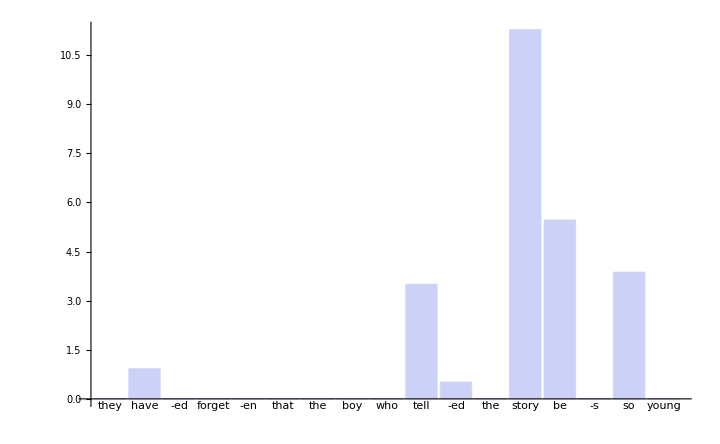

```mathematica
BarChart[entropyreductionsNew[[#]],ChartLabels->keenanhawkins[[#]],ImageSize->72*10]&/@{1}
```

### Word-by-Word Comparison

```mathematica
PairedBarChart[Style[entropyreductionsOld[[#]],Orange],Style[entropyreductionsNew[[#]],Purple],ImageSize->72*6,ChartLabels->korean[[#]]]&/@ Range[1,8]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}